```mathematica
b=0.4;
```

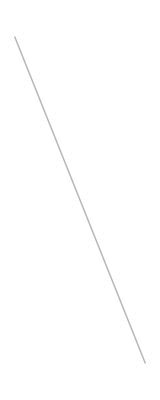

```mathematica
Graphics[{GrayLevel[0.7],Line[{{-10,10/b},{10,-10/b}}]}]
```

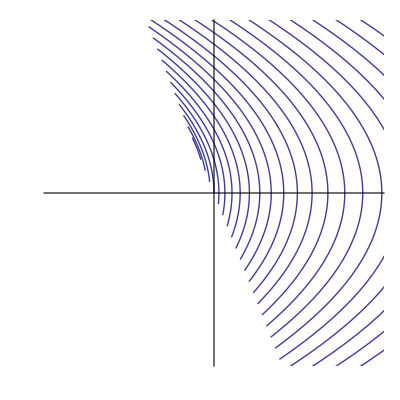

```mathematica
Show[Table[ParametricPlot[{y0^2/2-b y0-y^2/2,y},{y,b-Sqrt[b^2+y0^2-2b y0],b+Sqrt[b^2+y0^2-2b y0]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Ticks->None],{y0,0.5,4,0.1}]]
```

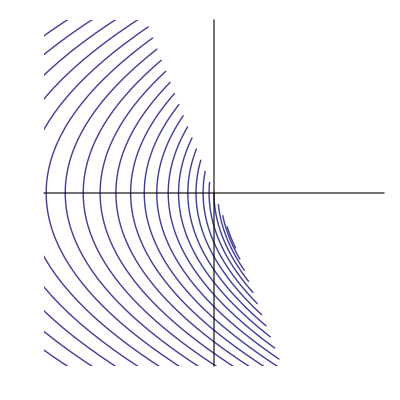

```mathematica
Show[Table[ParametricPlot[{-(y0^2/2-b y0-y^2/2),-y},{y,b-Sqrt[b^2+y0^2-2b y0],b+Sqrt[b^2+y0^2-2b y0]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Ticks->None],{y0,0.5,4,0.1}]]
```

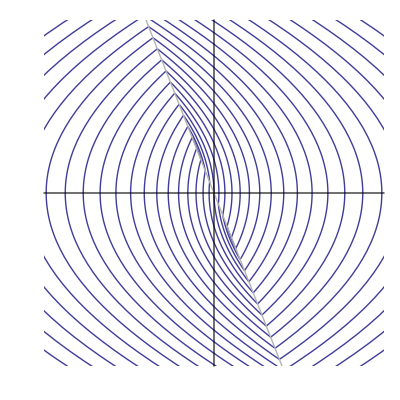

```mathematica
Show[%,%%,%%%]
```

```mathematica
phasediag[b_]:=Show[Table[ParametricPlot[{-(y0^2/2-b y0-y^2/2),-y},{y,b-Sqrt[b^2+y0^2-2b y0],b+Sqrt[b^2+y0^2-2b y0]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Ticks->None],{y0,0.5,4,0.1}],Table[ParametricPlot[{y0^2/2-b y0-y^2/2,y},{y,b-Sqrt[b^2+y0^2-2b y0],b+Sqrt[b^2+y0^2-2b y0]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Ticks->None],{y0,0.5,4,0.1}],Graphics[{{AbsoluteThickness[3],Line[{{-b^2,b},{b^2,-b}}]},{GrayLevel[0.7],Line[{{-10,10/b},{10,-10/b}}]}}]];
```

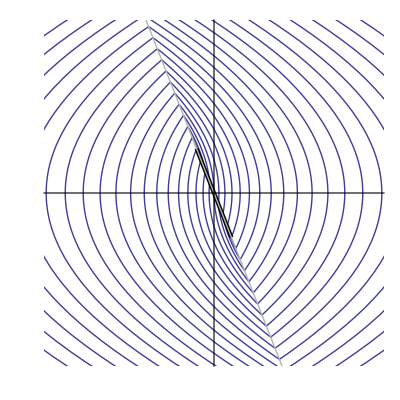

```mathematica
phasediag[0.4]
```

```mathematica
newphasediag:=Show[Join[Table[ParametricPlot[{a- y^2/2,y},{y,-Sqrt[a],2},PlotRange->{{-2,2},{-2,2}},Ticks->None],{a,0,4,0.15}],Table[ParametricPlot[{-a+ y^2/2,-y},{y,-Sqrt[a],2},PlotRange->{{-2,2},{-2,2}}],{a,0,4,0.15}],{ParametricPlot[{-y Abs[y]/2,y},{y,-2,2},PlotStyle->{Black,AbsoluteThickness[2]}]}]]
```

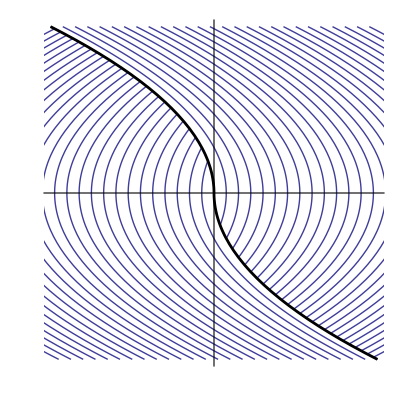

```mathematica
newphasediag
```